```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π, θ>-π};
```

```mathematica
f[zz_]:=c+k (zz+ⅈ d)^(θ/π+1);
c =-ⅈ d;
k = ⅇ^(ⅈ θ/2);
```

```mathematica
d=.4;
θ = 10*π/180;
```

```mathematica
lim={0,50d,-2d,0};
```

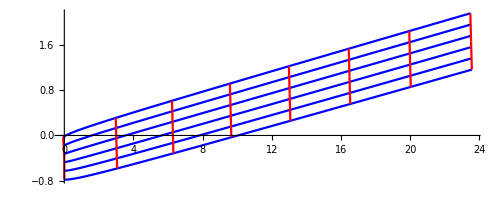

```mathematica
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]
```

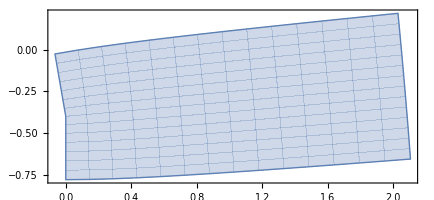

```mathematica
ParametricPlot[ReIm@f[ξ+ⅈ η],{ξ,lim⟦1⟧,lim⟦2⟧},{η,lim⟦3⟧,lim⟦4⟧}]
```